```mathematica
?QuantumWalks`*
```

```mathematica
?ExpValPosition
```

## Packages and nb definitions

```mathematica
Needs["QuantumWalks`"]
```

Ecuación (5), U(ρ,α)

```mathematica
c[ρ_,α_]:={{Exp[I*α]Sqrt[ρ],I*Sqrt[1-ρ]},{I*Sqrt[1-ρ],Exp[-I*α]Sqrt[ρ]}}
```

Caminata como yo entiendo que se hace en el artículo

```mathematica
ClearAll[DTQWFlitney2012]
DTQWFlitney2012[ψ0_,coinCombination_,reps_]:=Fold[Chop@ArrayPad[DTQWStep[#2[[1]],#2[[2]]].#1,2]&,ArrayPad[ψ0,2],Transpose[{Range[Length[coinCombination]*reps],Catenate[ConstantArray[coinCombination,reps]]}]]
```

## AB

```mathematica
ρ=1/2.;
α=0.005;
β=0.005;

A=c[ρ,α];
B=c[ρ,β];

coinCombination={A,B};
```

```mathematica
ψ0=N@Normalize[{1,-1}];
reps=50;

ψ=DTQWFlitney2012[ψ0,coinCombination,reps];

Chop[ExpValPosition[ψ,Length[coinCombination]*reps]]
```

-0.148213

```mathematica
expvalx=Table[
ψ=DTQWFlitney2012[ψ0,coinCombination,reps];
{reps,Chop[ExpValPosition[ψ,Length[coinCombination]*reps]]}
,{reps,0,100}];
```

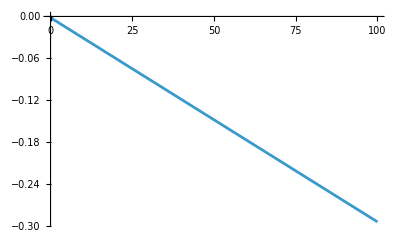

```mathematica
ListPlot[expvalx,
Joined->True]
```

## ABB

```mathematica
ρ=1/2.;
α=0.;
β=Pi/2.;

A=c[ρ,α];
B=c[ρ,β];

coinCombination={A,B,B};
```

```mathematica
ψ0=N@Normalize[{1,-1}];
reps=33;

ψ=DTQWFlitney2012[ψ0,coinCombination,reps];

Chop[ExpValPosition[ψ,Length[coinCombination]*reps]]
```

-9.656

## ABBB

```mathematica
ρ=1/2.;
α=0.01;
β=1.2;

A=c[ρ,α];
B=c[ρ,β];

coinCombination={A,B,B,B};
```

```mathematica
ψ0=N@Normalize[{1,-1}];
reps=25;

ψ=DTQWFlitney2012[ψ0,coinCombination,reps];

Chop[ExpValPosition[ψ,Length[coinCombination]*reps]]
```

-16.6787

## Fig. 4

```mathematica
t=10;
MapThread[ExpValPosition[#1,#2]&,{FoldList[Apply[ArrayPad[DTQWStep[#1,#2].#3,2]&,Append[#2,#1]]&,ArrayPad[ψ0,2],Transpose[{Range[t],Catenate[ConstantArray[{A,B},t/2]]}]],Range[0,t]}]
```

{0.,-0.00499998,-0.00499998,-0.00499998,-0.00749997,-0.00999996,-0.010625,-0.01125,-0.0134374,-0.0156249,-0.0164452}

```mathematica
t=10;
MapThread[ExpValPosition[#1,#2]&,{FoldList[Apply[ArrayPad[DTQWStep[#1,#2].#3,2]&,Append[#2,#1]]&,ArrayPad[ψ0,2],Transpose[{Range[t],Catenate[ConstantArray[{A,B},t/2]]}]],Range[0,t]}]
```

{0.,-0.00499998,-0.00499998,-0.00499998,-0.00749997,-0.00999996,-0.010625,-0.01125,-0.0134374,-0.0156249,-0.0164452}

```mathematica
ψ1=ArrayPad[DTQWStep[1,A].ArrayPad[ψ0,2],2]
ψ2=ArrayPad[DTQWStep[2,B].ψ1,2]
ψ3=ArrayPad[DTQWStep[3,A].ψ2,2]
ψ4=ArrayPad[DTQWStep[4,B].ψ3,2]
```

{0,0,0.+0. ⅈ,-0.499994+0.5025 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.499994-0.4975 ⅈ,0.+0. ⅈ,0,0}

{0,0,0.+0. ⅈ,-0.331606+0.375882 ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.355321-0.353549 ⅈ,0.351786+0.353549 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.374007-0.329952 ⅈ,0.+0. ⅈ,0,0}

{0,0,0.+0. ⅈ,-0.233149+0.266958 ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.265789-0.234481 ⅈ,0.499994-0.00249999 ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.499994-0.00249999 ⅈ,0.233312+0.264463 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.265626-0.231986 ⅈ,0.+0. ⅈ,0,0}

{0,0,0.+0. ⅈ,-0.153245+0.198314 ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.188768-0.164861 ⅈ,0.51861-0.210906 ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.175893+0.176774 ⅈ,0.177661-0.176774 ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.53981+0.142011 ⅈ,0.164039+0.187826 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.197325-0.152481 ⅈ,0.+0. ⅈ,0,0}

```mathematica
ρ=1/2.;
α=0.;
β=0.2;

A=c[ρ,α];
B=c[ρ,β];
```

```mathematica
expvalpos[[-10;;]]
```

{{91,0},{92,0},{93,0},{94,0},{95,0},{96,0},{97,0},{98,0},{99,0},{100,0}}

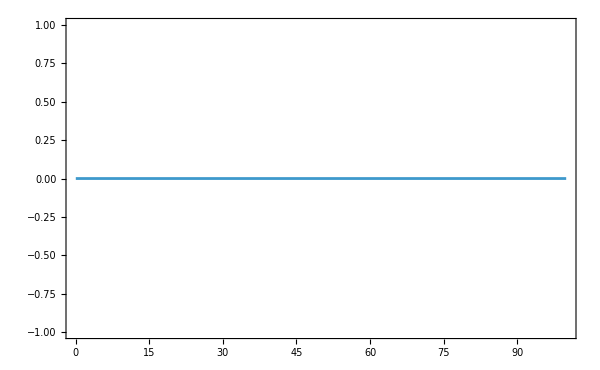

```mathematica
t=100;
ψ0=N@Normalize[{1,-1}];
expvalpos=MapThread[{#2,Chop@ExpValPosition[#1,#2]}&,{FoldList[ArrayPad[DTQWStep[#2[[1]],#2[[2]]].#1,2]&,ArrayPad[ψ0,2],Transpose[{Range[t],Catenate[ConstantArray[{A,B},t/2]]}]],Range[0,t]}];
ListPlot[expvalpos,
Joined->True,
PlotRange->All,
Joined->True,
PlotRange->{{0,1000},{-2,1.5}},
Frame->True,
FrameStyle->Directive[Black,FontSize->22],
ImageSize->600
]
```

```mathematica
t=2;
FoldList[ArrayPad[f[#2[[1]],#2[[2]]].#1,2]&,x0,Transpose[{Range[t],Catenate[ConstantArray[{a,b},t/2]]}]]
```

ArrayPad::arr: First argument f[1,a].x0 to ArrayPad should be an array.

ArrayPad::arr: First argument f[2,b].f[1,a].x0 to ArrayPad should be an array.

{x0,f[1,a].x0,f[2,b].f[1,a].x0}

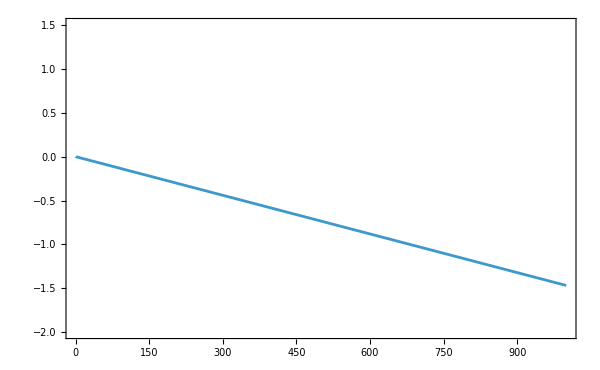

```mathematica
t=1000;
ψ0=N@Normalize[{1,-1}];
expvalpos=MapThread[{#2,Chop@ExpValPosition[#1,#2]}&,{FoldList[ArrayPad[DTQWStep[#2,A].#1,2]&,ArrayPad[ψ0,2],Range[t]],Range[0,t]}];
ListPlot[expvalpos,
Joined->True,
PlotRange->{{0,1000},{-2,1.5}},
Frame->True,
FrameStyle->Directive[Black,FontSize->22],
ImageSize->600
]
```

```mathematica
t=2;
ShiftFlitney[t_]:=SparseArray[
    Join[
      Table[{i, i + 2}, {i, Range[1, # - 2, 2]}], 
      Table[{i, i - 2}, {i, Range[4, #, 2]}]
    ] -> 1., {#, #}] &[2*(2*t + 1)]
```

```mathematica
DTQWStepFlitney[t_, c_] := ShiftFlitney[t] . Coin[t, c]
```

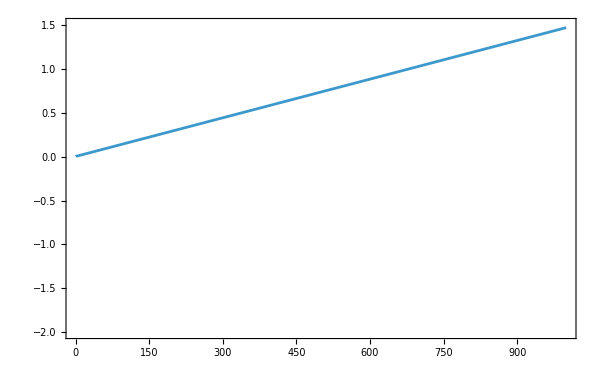

```mathematica
t=1000;
ψ0=N@Normalize[{1,-1}];
expvalpos=MapThread[{#2,Chop@ExpValPosition[#1,#2]}&,{FoldList[ArrayPad[DTQWStepFlitney[#2,A].#1,2]&,ArrayPad[ψ0,2],Range[t]],Range[0,t]}];
ListPlot[expvalpos,
Joined->True,
PlotRange->{{0,1000},{-2,1.5}},
Frame->True,
FrameStyle->Directive[Black,FontSize->22],
ImageSize->600
]
```

### To erase

```mathematica
?ExpValPosition
```